```mathematica
(*example discrete rwd data for time-dependent decreasing task*)
data={{0.5,10},{1,5},{2,3},{4,2},{5,1},{6,0.5}};
```

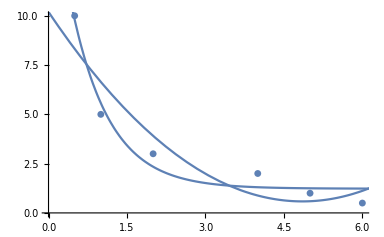

```mathematica
(*2 fitting funcs for data*)
Show[ListPlot[data],Plot[Exp[-1.361x+2.829]+1.23,{x,-1,10}],Plot[10.198-3.961 x+0.408 x^2,{x,0,10}]]
```

```mathematica
FindFit[data, Exp[a x+b]+c,{a,b,c},x]
```

{a→-1.36157,b→2.8293,c→1.22999}

```mathematica
FindFit[data, a+b x+c x^2,{a,b,c},x]
```

{a→10.198,b→-3.96126,c→0.408452}

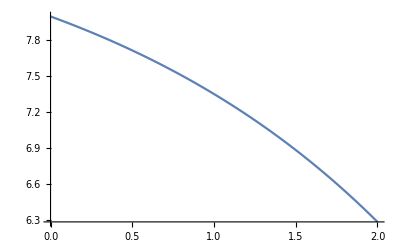

```mathematica
(*example of rwd func of fixed-ddl tasks, concave func*)
Plot[10-(1*Exp[0.5*x]+1),{x,0,2}]
```

```mathematica
(*find fitting rwd func for asap task*)
app=10;rwd=5;
data={{0,rwd},{app*1.4,rwd/2},{app*2.5,rwd/5}};
FindFit[data, a Exp[-b x]+rwd-a,{a,b,c},x]
```

General::munfl: -11.25/(-7.98120765338625×10^2798008) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

{a→3.25,b→14193.5,c→1.}

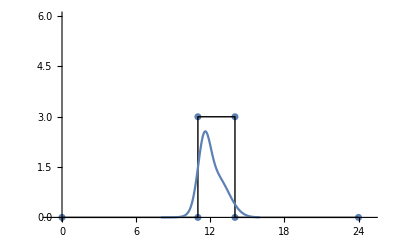

```mathematica
(*rwd func for meal*)
rwd=3;
data={{0,0},{11,0},{11,rwd},{14,rwd},{14,0},{24,0}};
Show[ListPlot[data,PlotRange->{{-1,25},{0,6}}],Graphics[Line[data]],Plot[0.6*rwd*Exp[-(x-11.5)^2/(2*0.5^2)]+0.4*rwd*Exp[-(x-12.5)^2/(2*1^2)],{x,8,16}]]
```

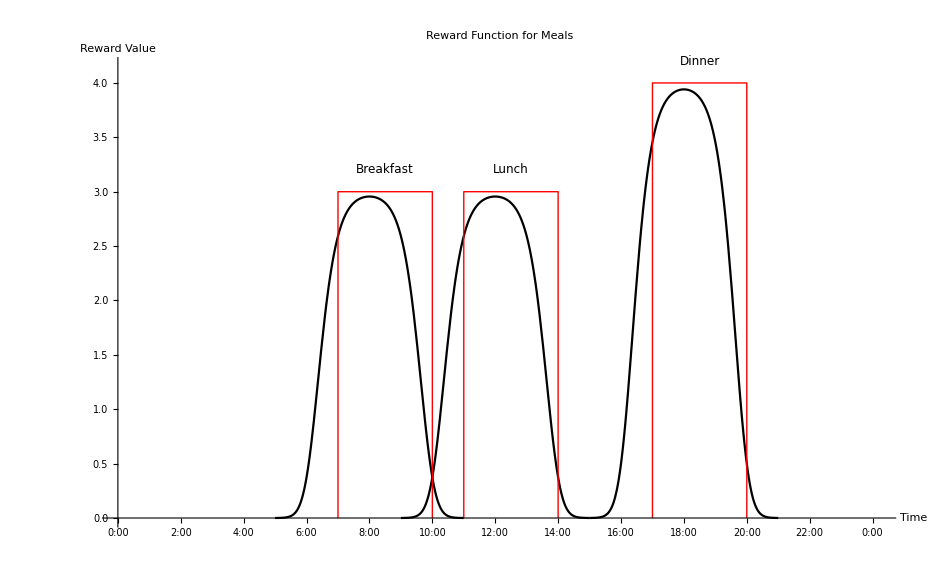

```mathematica
(*new rwd func for meal: generalised logistic func*)
(*logistic contribution: y=1/(1+e^(-(x-u)/b))^a*)
(*logistic sigmoid: y=1/(1+e^-x)*)
meal[x_,l_,r_, rwd_]:=rwd*LogisticSigmoid[(x-l+1)*3]^3+rwd*LogisticSigmoid[(r-x)*3]^3-rwd
data={{0,0},{early,0},{early,rwd},{late,rwd},{late,0},{24,0}};
Show[Plot[meal[x,7,10,3],{x,5,11}, PlotStyle->Black],Plot[meal[x,11,14,3],{x,9,15}, PlotStyle->Black],Plot[meal[x,17,20,4],{x,15,21}, PlotStyle->Black],Graphics[{Red,Line[{{7,0},{7,3},{10,3},{10,0}}]}],Graphics[{Red,Line[{{11,0},{11,3},{14,3},{14,0}}]}],Graphics[{Red,Line[{{17,0},{17,4},{20,4},{20,0}}]}],Graphics[{Text[Style["Breakfast",12],{8.5,3.2}],Text[Style["Lunch",12],{12.5,3.2}],Text[Style["Dinner",12],{18.5,4.2}]}],  PlotRange->{{0,24.25},{0,4.15}},AxesOrigin->{0,0},AxesStyle->{{Directive[Black, 12],Arrowheads[0.015]},{Directive[Black, 12],Arrowheads[0.015]}}, PlotLabel->"Reward Function for Meals",AxesLabel->{"Time", "Reward Value"},Ticks->{Array[{#,ToString[Mod[#,24]]<>":00"}&,25,0],Automatic},  LabelStyle->Directive[Black,13,Thick]]
```

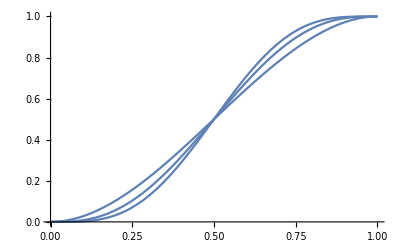

```mathematica
(*smoothstep func*)
Show[Plot[-2 x^3+3 x^2,{x,0,1}],Plot[6 x^5-15 x^4+10 x^3,{x, 0, 1}], Plot[-20 x^7+70 x^6-84 x^5+35 x^4,{x,0,1}]]
```

```mathematica
(*rwd func for sleeping*)
dur[x_, durMin_, durMax_, rwd_]:=Piecewise[{{rwd*(1-Exp[-0.8(x-durMin)]),durMin≤x≤durMax},{0,x<durMin},{0,x>durMax}}];
bed[x_,bedMin_,bedMax_,rwd_]:=Piecewise[{{rwd*Exp[-x+bedMin],bedMin≤x≤24},{rwd*Exp[-x-24+bedMin],0≤x≤bedMax},{0,bedMax≤x≤bedMin}}];
sleep[durx_,bedx_]:=Sqrt[dur[durx,durMin,durMax,rwd]*bed[bedx,bedMin,bedMax, rwd]];
durMin=5;durMax=12;bedMin=-2;bedMax=4;rwd=5;
bedPlot[x_, bedMin_, bedMax_, rwd_]:=Piecewise[{{rwd*Exp[-x+bedMin],bedMin≤x≤bedMax},{0,x≤bedMin},{0,x≥bedMax}}];
sleepPlot[durx_,bedx_]:=Sqrt[dur[durx,durMin,durMax,rwd]*bedPlot[bedx,bedMin,bedMax, rwd]];
Plot3D[sleepPlot[durx,bedx],{durx,durMin, durMax},{bedx,bedMin, bedMax},AxesLabel->{"Duration/hours", "Bedtime","Reward Value"},ColorFunction->"Rainbow",AxesStyle->Directive[Black,12],PlotLabel->"3D Function of bedtime and sleeping duration", LabelStyle->Directive[Black, 13, Thick],Ticks->{Array[#&,8,5],Array[{#,ToString[Mod[#+24,24]]<>":00"}&,7,-2],Automatic}]
```

-Graphics3D-

```mathematica
Array[sleepPlot[12,#]&,8,-2]
```

{4.99075,3.02704,1.83599,1.11359,0.675424,0.409665,0.248475,0.}

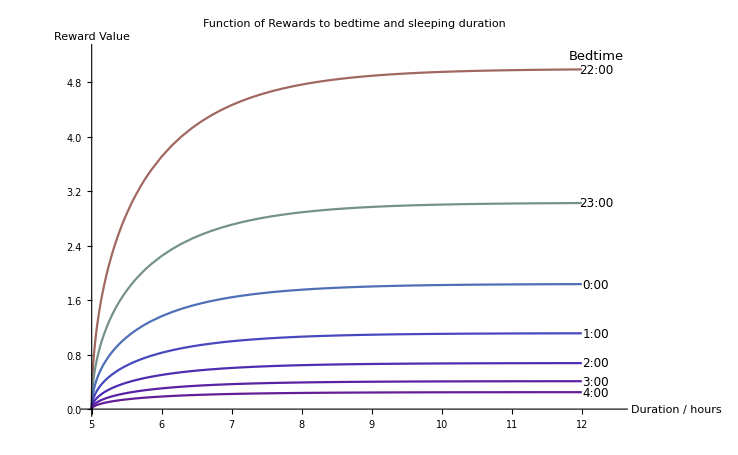

```mathematica
(*funcs for bedtime and duration*)
Show[Plot[{sleepPlot[durx,-2],sleepPlot[durx,-1],sleepPlot[durx,0],sleepPlot[durx,1],sleepPlot[durx,2],sleepPlot[durx,3],sleepPlot[durx,4]},{durx,5,12},AxesOrigin->{5,0},PlotRange->{{5,12.5},{0,5.25}},PlotLabel->"Function of Rewards to bedtime and sleeping duration",LabelStyle->Directive[Black, 13, Thick],AxesStyle->{{Directive[Black,12],Arrowheads[0.015]},{Directive[Black,12],Arrowheads[0.015]}},AxesLabel->{"Duration / hours","Reward Value"}, Ticks->Automatic, ColorFunction->"Rainbow"],Graphics[Text[Style["Bedtime",13],{12.2,5.2}]], 
Graphics[Text[Style["22:00",12],{12.2,4.99}]], Graphics[Text[Style["23:00",12],{12.2,3.03}]],  Graphics[Text[Style["0:00",12],{12.2,1.83}]], Graphics[Text[Style["1:00",12],{12.2,1.11}]], Graphics[Text[Style["2:00",12],{12.2,0.68}]], Graphics[Text[Style["3:00",12],{12.2,0.41}]], Graphics[Text[Style["4:00",12],{12.2,0.24}]]]
```

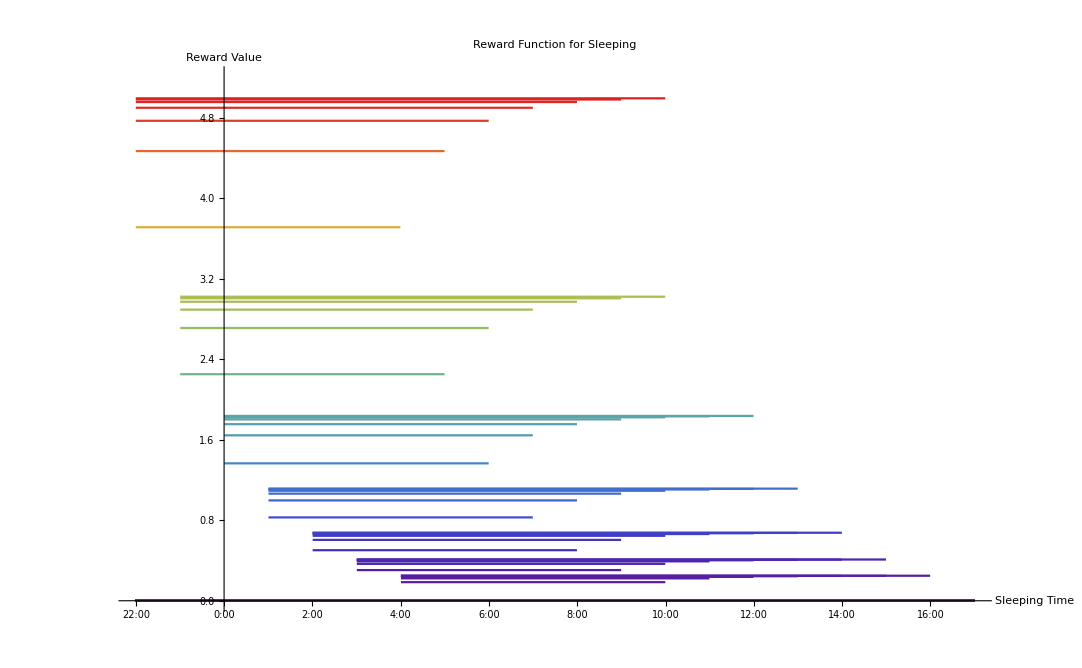

```mathematica
(*plot rwd func for sleeping*)
Show[Plot[{Piecewise[{{sleep[5,22],-2≤x≤3}}],Piecewise[{{sleep[6,22],-2≤x≤4}}],Piecewise[{{sleep[7,22],-2≤x≤5}}],Piecewise[{{sleep[8,22],-2≤x≤6}}],Piecewise[{{sleep[9,22],-2≤x≤7}}],Piecewise[{{sleep[10,22],-2≤x≤8}}],Piecewise[{{sleep[11,22],-2≤x≤9}}],Piecewise[{{sleep[12,22],-2≤x≤10}}],Piecewise[{{sleep[5,23],-1≤x≤4}}],Piecewise[{{sleep[6,23],-1≤x≤5}}],Piecewise[{{sleep[7,23],-1≤x≤6}}],Piecewise[{{sleep[8,23],-1≤x≤7}}],Piecewise[{{sleep[9,23],-1≤x≤8}}],Piecewise[{{sleep[10,23],-1≤x≤9}}],Piecewise[{{sleep[11,23],-1≤x≤10}}],Piecewise[{{sleep[12,23],-1≤x≤11}}]Piecewise[{{sleep[5,0],0≤x≤5}}],Piecewise[{{sleep[6,0],0≤x≤6}}],Piecewise[{{sleep[7,0],0≤x≤7}}],Piecewise[{{sleep[8,0],0≤x≤8}}],Piecewise[{{sleep[9,0],0≤x≤9}}],Piecewise[{{sleep[10,0],0≤x≤10}}],Piecewise[{{sleep[11,0],0≤x≤11}}],Piecewise[{{sleep[12,0],0≤x≤12}}],Piecewise[{{sleep[5,1],1≤x≤6}}],Piecewise[{{sleep[6,1],1≤x≤7}}],Piecewise[{{sleep[7,1],1≤x≤8}}],Piecewise[{{sleep[8,1],1≤x≤9}}],Piecewise[{{sleep[9,1],1≤x≤10}}],Piecewise[{{sleep[10,1],1≤x≤11}}],Piecewise[{{sleep[11,1],1≤x≤12}}],Piecewise[{{sleep[12,1],1≤x≤13}}],Piecewise[{{sleep[5,2],2≤x≤7}}],Piecewise[{{sleep[6,2],2≤x≤8}}],Piecewise[{{sleep[7,2],2≤x≤9}}],Piecewise[{{sleep[8,2],2≤x≤10}}],Piecewise[{{sleep[9,2],2≤x≤11}}],Piecewise[{{sleep[10,2],2≤x≤12}}],Piecewise[{{sleep[11,2],2≤x≤13}}],Piecewise[{{sleep[12,2],2≤x≤14}}],Piecewise[{{sleep[5,3],3≤x≤8}}],Piecewise[{{sleep[6,3],3≤x≤9}}],Piecewise[{{sleep[7,3],3≤x≤10}}],Piecewise[{{sleep[8,3],3≤x≤11}}],Piecewise[{{sleep[9,3],3≤x≤12}}],Piecewise[{{sleep[10,3],3≤x≤13}}],Piecewise[{{sleep[11,3],3≤x≤14}}],Piecewise[{{sleep[12,3],3≤x≤15}}],Piecewise[{{sleep[5,4],4≤x≤9}}],Piecewise[{{sleep[6,4],4≤x≤10}}],Piecewise[{{sleep[7,4],4≤x≤11}}],Piecewise[{{sleep[8,4],4≤x≤12}}],Piecewise[{{sleep[9,4],4≤x≤13}}],Piecewise[{{sleep[10,4],4≤x≤14}}],Piecewise[{{sleep[11,4],4≤x≤15}}],Piecewise[{{sleep[12,4],4≤x≤16}}],Piecewise[{{sleep[5,5],5≤x≤10}}],Piecewise[{{sleep[6,5],5≤x≤11}}],Piecewise[{{sleep[7,5],5≤x≤12}}],Piecewise[{{sleep[8,5],5≤x≤13}}],Piecewise[{{sleep[9,5],5≤x≤14}}],Piecewise[{{sleep[10,5],5≤x≤15}}],Piecewise[{{sleep[11,5],5≤x≤16}}],Piecewise[{{sleep[12,5],5≤x≤17}}]},{x,-2,17},PlotRange->{Full,{0,5.2}},AxesOrigin->{0,0}, Ticks->{Array[{#,ToString[Mod[#,24]]<>":00"}&,20,-2],Automatic}, AxesLabel->{"Sleeping Time","Reward Value"},PlotLabel->"Reward Function for Sleeping", LabelStyle->{Directive[Black,13,Thick]}, TicksStyle->Directive[Black], AxesStyle->{{Directive[Black, 12],Arrowheads[0.01]},{Directive[Black, 12],Arrowheads[0.01]}},ColorFunction->"Rainbow"]]
```

```mathematica
strict[strictness_,prod_,enjoy_]:=strictness*prod+(1-strictness)*enjoy;
```

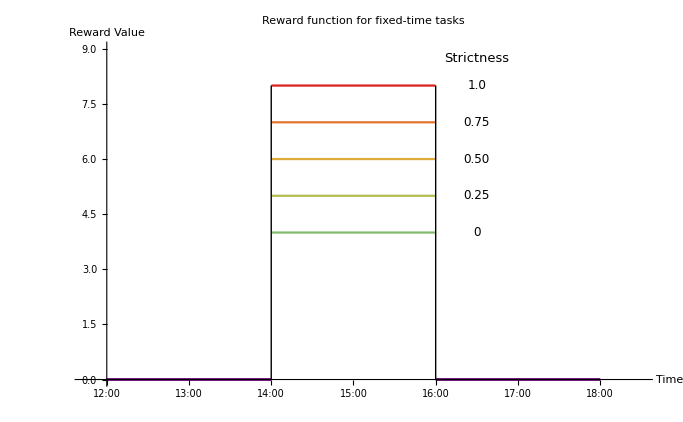

```mathematica
Show[Plot[Array[Piecewise[{{strict[#/4,8,4],14≤x≤16}}]&,5,0],{x,12,18},ColorFunction->"Rainbow",AxesStyle->{{Directive[Black,12],Arrowheads[0.02]},{Directive[Black,12],Arrowheads[0.02]}},PlotRange->{{11.75,18.5},{0,9}},AxesOrigin->{12,0},AxesLabel->{"Time","Reward Value"}, PlotLabel->"Reward function for fixed-time tasks",LabelStyle->Directive[Black,13,Thick],Ticks->{Array[{#,ToString[#]<>":00"}&,7,12],Automatic}],Graphics[Line[{{14,0},{14,8}}]],Graphics[Line[{{16,0},{16,8}}]],Array[Graphics[Text[Style[ToString[N[#/4,2]],12],{16.5,4+#}]]&,5,0],Graphics[Text[Style["Strictness",13],{16.5,8.75}]]]
```

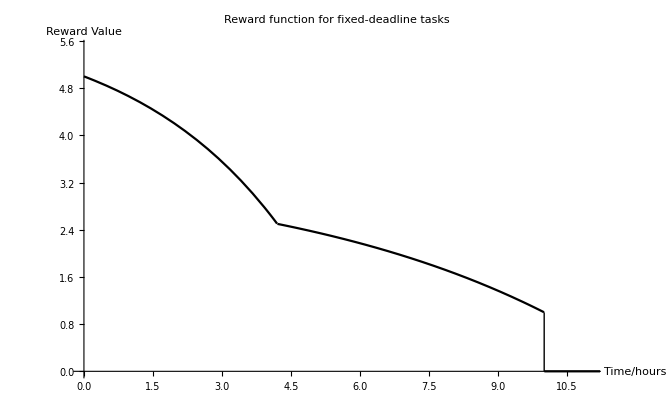

```mathematica
(*rwd func for fixed-ddl tasks*)
findDDL[x_,p1x_,p1y_,p2x_,p2y_]:=p1y+1-Exp[Log[p1y+1-p2y]/(p2x-p1x)*(x-p1x)];
appTime=3*1.4;ddl=10;rwd=5;
points={{0,rwd},{appTime,rwd/2},{ddl,rwd/5}};
Show[Plot[Piecewise[{{findDDL[x,0,rwd,appTime,rwd/2],0≤x≤appTime},{findDDL[x,appTime,rwd/2,ddl,rwd/5],appTime≤x≤ddl},{0,x≥ddl}}],{x,0,ddl+2},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->{{0,11},{0,5.5}},AxesStyle->{{Directive[Black,12],Arrowheads[0.02]},{Directive[Black,12],Arrowheads[0.02]}},PlotLabel->"Reward function for fixed-deadline tasks",AxesLabel->{"Time/hours","Reward Value"},LabelStyle->Directive[Black,13,Thick]],Graphics[Line[{{ddl,rwd/5},{ddl,0}}]]]
```

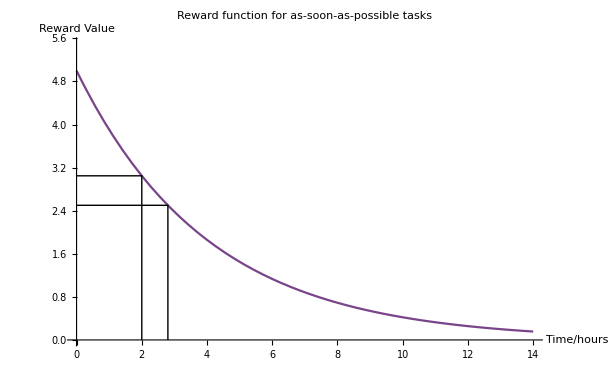

```mathematica
asap[x_,p1x_,p1y_,p2x_,p2y_]:=p1y*Exp[-Log[p1y/p2y]/(p2x-p1x)*(x-p1x)];
appTime=2*1.4;rwd=5;
Show[Plot[asap[x,0,rwd,appTime,rwd/2],{x,0,appTime*5},ColorFunction->"Rainbow", PlotLabel->"Reward function for as-soon-as-possible tasks", LabelStyle->Directive[Black, 13, Thick],AxesLabel->{"Time/hours", "Reward Value"}, AxesStyle->{{Directive[Black,12],Arrowheads[0.02]},{Directive[Black,12],Arrowheads[0.02]}},PlotRange->{{0,14},{0,rwd+0.5}},AxesOrigin->{0,0}],Graphics[Line[{{appTime,0},{appTime,rwd/2},{0,rwd/2}}]],Graphics[Line[{{2,0},{2,asap[2,0,rwd,appTime,rwd/2]},{0,asap[2,0,rwd,appTime,rwd/2]}}]]]
```

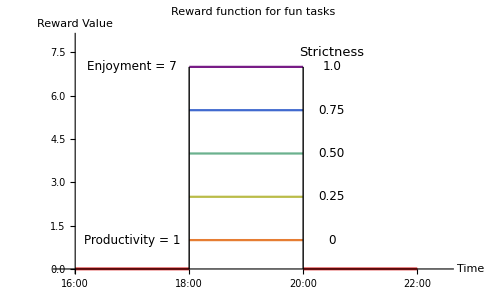

```mathematica
Show[Plot[Array[Piecewise[{{strict[#/4,1,7],18≤x≤20}}]&,5,0],{x,16,22},AxesStyle->{{Directive[Black,12],Arrowheads[0.02]},{Directive[Black,12],Arrowheads[0.02]}},PlotRange->{{15.75,22.5},{0,8}},AxesOrigin->{16,0},AxesLabel->{"Time","Reward Value"}, PlotLabel->"Reward function for fun tasks",LabelStyle->Directive[Black,13,Thick],Ticks->{Array[{#,ToString[#]<>":00"}&,7,16],Automatic},ColorFunction->ColorData[{"Rainbow","Reverse"}]],Graphics[Line[{{20,0},{20,7}}]],Graphics[Line[{{18,0},{18,7}}]],Array[Graphics[Text[Style[ToString[N[#/4,2]],12],{20.5,1+1.5*#}]]&,5,0],Graphics[Text[Style["Strictness",13],{20.5,7.5}]],Graphics[Text[Style["Productivity = 1",12],{17,1}]],Graphics[Text[Style["Enjoyment = 7",12],{17,7}]]]
```